```mathematica
energies={}
```

{}

```mathematica
Λ[x_]=0.3127477*x-0.0231669*x^2-0.0005110 x^3-0.0000045 x^4;
```

10

3

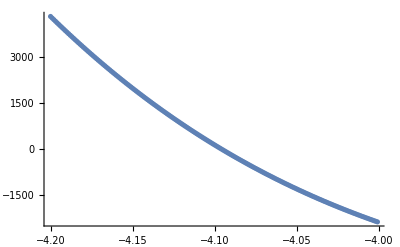

```mathematica
R=10
Distance=3;
minC=-4.2;
maxC=-4;
list={};
list2={};
step=0.001;
Print[Distance];
For[c=minC,c≤maxC,c+=step,
sol=NDSolve[{(ξ^2-1)D[g[ξ],{ξ,2}]+2ξ D[g[ξ],ξ]+(2*Distance* ξ +c ξ^2-Λ[c])g[ξ]==0,g[1.000001]==1,g'[1.000001]==(c-Λ[c])/2},g,{ξ,1.000001,R}];
temp[ξ_]=g[ξ]/.sol;
AppendTo[list, temp[R]];
AppendTo[list2, c];
];
xy=Thread @ {list2,Flatten[list]};
int=Interpolation[xy];
theC=x/.FindRoot[int[x]==0,{x,minC}];
ListPlot[xy]
```

```mathematica
theC
```

-4.09599

```mathematica
4*theC/Distance^2
```

-2.19609

InterpolatingFunction[…][ξ]

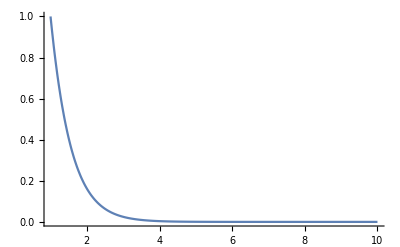

```mathematica
c=theC;
sol=First[NDSolve[{(ξ^2-1)D[g[ξ],{ξ,2}]+2ξ D[g[ξ],ξ]+(2*Distance* ξ +c ξ^2-Λ[c])g[ξ]==0,g[1.000001]==1,g'[1.000001]==(c-Λ[c])/2},g,{ξ,1.000001,R}]];
r[ξ_]=g[ξ]/.sol
Plot[r[ξ]/.sol,{ξ,1.000001, R},PlotRange->All]
```

```mathematica
(*angular equation*)
c=theC;
phiSol=First[NDSolve[{(1-η^2)D[f[η],{η,2}]-2η D[f[η],η]-(-Λ[c]+c η^2)f[η]==0,f[0.999999999]==1,f[-0.999999999]==1},f,{η,-0.999999999,0.999999999}]]
```

{f→InterpolatingFunction[…]}

InterpolatingFunction[…][η]

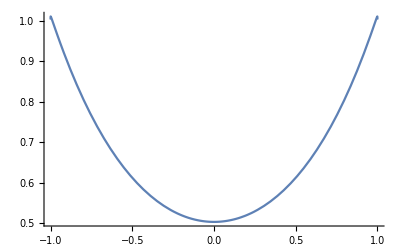

```mathematica
angSol[η_]=f[η]/.phiSol
Plot[angSol[η],{η,-1,1},PlotRange->All]
```

```mathematica
NIntegrate[angSol[η]^2,{η,-0.999999999,0.999999999}]
```

0.915984

```mathematica
NIntegrate[angSol[η]^2 r[ξ]^2 Distance^3/8(ξ^2-η^2),{ξ,1.000001,R},{η,-0.999999999,0.999999999}]
```

1.05445

```mathematica
ra[x_,z_]=√((z+Distance/2)^2+x^2);
rb[x_,z_]=√((z-Distance/2)^2+x^2);
ξ[x_,z_]=(ra[x,z]+rb[x,z])/Distance;
η[x_,z_]=(ra[x,z]-rb[x,z])/Distance;
ψ[ξ_,η_]=r[ξ]*angSol[η]
```

InterpolatingFunction[…][η] InterpolatingFunction[…][ξ]

```mathematica
Plot3D[ψ[ξ,η],{ξ,1.00001, 10},{η,-0.999,0.999},PlotRange->All]
```

-Graphics3D-

```mathematica
ξ[0,0]
η[0,0]
```

1

0

```mathematica
ψ[1,0]
```

91290.5

```mathematica
Ψ1[x_,z_]=ψ[ξ[x,z],η[x,z]]
```

InterpolatingFunction[…][1/3 (-√(x^2+(-3/2+z)^2)+√(x^2+(3/2+z)^2))] InterpolatingFunction[…][1/3 (√(x^2+(-3/2+z)^2)+√(x^2+(3/2+z)^2))]

```mathematica
Plot3D[Ψ1[x,z],{x,-5,5},{z,-5,5},PlotRange->All]
```

-Graphics3D-

```mathematica
energies={};
For[i=1,i<=10,i+=1,
Distance=i;
minC=-30;
maxC=-0.5;
list={};
list2={};
step=0.001;
Print[Distance];
For[c=minC,c≤maxC,c+=step,
sol=NDSolve[{(ξ^2-1)D[g[ξ],{ξ,2}]+2ξ D[g[ξ],ξ]+(2*Distance* ξ +c ξ^2-Λ[c])g[ξ]==0,g[1.000001]==1,g'[1.000001]==(c-Λ[c])/2},g,{ξ,1.000001,R}];
temp[ξ_]=g[ξ]/.sol;
AppendTo[list, temp[R]];
AppendTo[list2, c];
];
xy=Thread @ {list2,Flatten[list]};
int=Interpolation[xy];
theC=x/.FindRoot[int[x]==0,{x,-2}];
AppendTo[energies, 4*theC/Distance^2]
]
```

```mathematica
R=20
Distance=2;
minC=-2.4;
maxC=-2;
list={};
list2={};
step=0.0001;
Print[Distance];
For[c=minC,c≤maxC,c+=step,
sol=NDSolve[{(1-η^2)D[f[η],{η,2}]-2η D[f[η],η]-(-Λ[c]+c η^2)f[η]==0,f[-0.999999999]==1,f'[-0.999999999]==-(c-Λ[c])/2},f,{η,-1,1}];
temp[η_]=f[η]/.sol;
AppendTo[list, temp[-1]];
AppendTo[list2, c];
];
xy=Thread @ {list2,Flatten[list]};
int=Interpolation[xy];
theC=x/.FindRoot[int[x]==1,{x,minC}];
ListPlot[xy,PlotRange->{-2,2}]
```

```mathematica
Λ[-1]
```

-0.335408